## Benchmark Continuous Wavelet Transform

## Generate data

```mathematica
n = 100000;
y[x_]:=Sin[2*π*(1+(7*x)/n)*x/64];
data = Table[y[x],{x,0,n}];
```

## Perform Continuous Wavelet Transform

```mathematica
(AbsoluteTiming[For[i=0,i<10,i++,ContinuousWaveletTransform[data,MorletWavelet[],{6,500}]]]/10)[[1]]
```

39.2974

## Example of Morlet wavelet

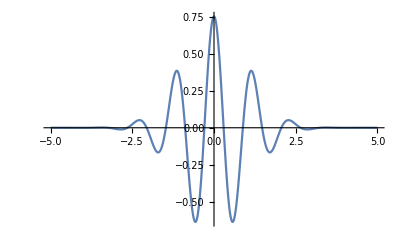

```mathematica
Plot[WaveletPsi[MorletWavelet[],x],{x,-5,5},PlotRange->All]
```